```mathematica
Osservazione: si puó automatizzare la ricerca della biforcazione.
Per determinare la biforcazione n-esima si parte da un appropriato valore di μ inferiore a quello di boforcazione (stimato ad occhio) e si confrontano, per un opportunamente grande N, le iterate N-esima e (N+2^n)-esima di uno stesso punto inziale. Se sono molto vicini non siamo ancora alla biforcazione, e bisogna aumentare μ. Appena cominciano ad allontanarsi siamo arrivati alla biforcazione.
```

```mathematica
f[μ_,x_]:= μ x(1-x)
fn[μ_,x_,n_]:=Nest[f[μ,#]&,x,n]
check[x0_,μ_,nstart_]:= Mean[Differences[fn[x0,μ,nstart+2^#]&/@Range[5]]]
```

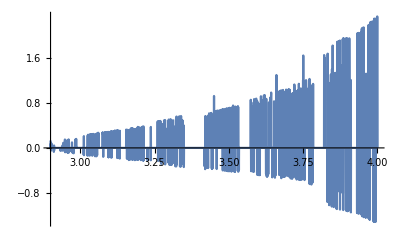

```mathematica
Plot[10^6 check[1/x,x,10]==0,{x,2.9,4}]
```

```mathematica
data= ParallelTable[{μ,Chop[10^6 check[1/μ,μ,10]]},{μ,2.8,4,10^-5}];
```

Partiziono la lista in liste più piccole così da poterci andare preciso.
la prima è da 2.8 a 3.2 circa
la lista è lunga 120.000

e va da 2.8 a 4 (lunga 1.2) ergo ogni .1 corrisponde a 10.000 tick
il primo scaglione è 2.8->3.2, il secondo 3.2->3.55, il terzo 3.55->3.65, il quarto 3.65->3.7 e butto il resto nel quinto.
ergo traducendo il primo è lungo 0.4, il secondo 0.35, il terzo 0.1, il quarto 0.05
ergo 40.000 tick, 35.000, 10.000,5.000

```mathematica
manualseparate[list_,seps_]:= Take[list,#]&/@({seps[[#]]+1,seps[[#+1]]}&/@Range[Length[seps]-1])
```

```mathematica
datatot=manualseparate[data0,{0,4,7.5,8.5,9,12}10^4];
```

```mathematica
ddata[x_]:=datatot⟦x⟧⟦#⟧&/@SequencePosition[datatot⟦x⟧,Table[{_,0},25-2x],Overlaps->False]
```

```mathematica
positions=First/@(First/@Flatten[ddata[#]&/@Range[Length[datatot]],1])
```

#### reimporto il codice per attrattivoplot

```mathematica
attrattivoPlot[nx_,n_,η_]:=With[{f=Compile[{{μ,_Real},{x,_Real}},μ x(1.-x)]},
ListPlot[
Union@Flatten[Table[
ParallelTable[
{μ,FixedPoint[Chop[f[μ,#]]&,x0,n]},{μ,Subdivide[0,4.,η]}],
{x0,Subdivide[0,1.,nx]}
],1],
PlotStyle->{AbsolutePointSize[0.015],Black},
PlotRange->{{0,4},{0,1}},
Ticks->{Subdivide[0,4.,20],Subdivide[0,1.,10]}
]
]
```

```mathematica
separazioni= attrattivoPlot[30,10^4,10^4]
```

```mathematica
Show[{separazioni,ParametricPlot[{#,y},{x,0,4},{y,0,1}]&/@positions}]
```

```mathematica
μ[n_]:=separazioni⟦n⟧
```

```mathematica
ListPlot[Table[(μ[n]-μ[n-1])/(μ[n+1]-μ[n]),{n,2,6}]](*idealmente*)
```